```mathematica
<<MaTeX`
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

{2+6 p-10 p^2+8 p^3-4 p^4,4-2 p-3 p^2+8 p^3-2 p^4,5-8 p+9 p^2-2 p^4,5-8 p+8 p^2}

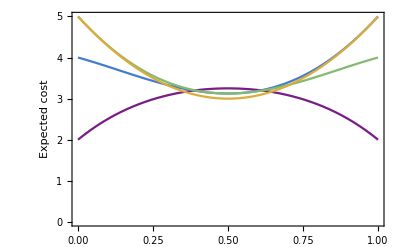

Piecewise[{{5-8 p+8 p^2, Root0.356Root[3-14 #1+18 #1^2-8 #1^3+4 #1^4&,1]0.3561576120381933≤p≤Root0.644Root[3-14 #1+18 #1^2-8 #1^3+4 #1^4&,2]0.6438423879618067}, {-2 (-1-3 p+5 p^2-4 p^3+2 p^4), True}}]

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3.16553,{p→0.356158}}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3.16553,{p→0.643842}}

1.19836

-2.30148

{{p→Root0.356Root[3-14 #1+18 #1^2-8 #1^3+4 #1^4&,1]0.3561576120381933},{p→Root0.644Root[3-14 #1+18 #1^2-8 #1^3+4 #1^4&,2]0.6438423879618067}}

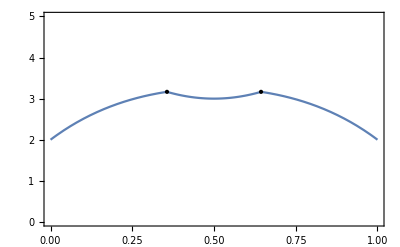

```mathematica
P0[p_]=5p^0+-8p^1+8p^2+0p^3+0p^4+0p^5;
P2[p_]=5p^0+-8p^1+9p^2+0p^3+-2p^4+0p^5;
P12[p_]=4p^0+-2p^1+-3p^2+8p^3+-2p^4+0p^5;
P38[p_]=2p^0+6p^1+-10p^2+8p^3+-4p^4+0p^5;

d = {P38[p],P12[p],P2[p],P0[p]}
Plot[{P38[p],P12[p],P2[p],P0[p]},{p,0,1},Axes ->True,PlotLegends->{MaTeX@"P_1(p)", MaTeX@"P_2(p)", MaTeX@"P_3(p)", MaTeX@"P_4(p)"},PlotStyle->ColorData["Rainbow"]/@(Range[0,Length@d]/Length@d),Frame -> True,FrameLabel->{MaTeX@"p", "Expected cost"},LabelStyle->{Black,Medium} ,PlotRange->{{0,1},{0,5}}]

f[p_]=Expand[PiecewiseExpand[FullSimplify[Min[d],0<p<1]]]
{max1,pmax1} = FindMaximum[f[p],{p,0.4}]
{max2,pmax2} = FindMaximum[f[p],{p,0.6}]
Limit[f'[p],p->{p/.pmax1},Direction->"FromBelow"]
Limit[f'[p],p->{p/.pmax1}+0.0000000001,Direction->"FromAbove"]
Solve[FunctionSingularities[f[p],p,Reals]&&0<p<1,p,Reals]
Plot[f[p],{p,0,1},PlotLegends->"Expressions",Epilog->{PointSize->Large,Point[{p,3.165525060596445}]/. %},Frame -> True,FrameLabel->{MaTeX@"p", MaTeX@"D_p(f)"},LabelStyle->{Black,Medium} ,PlotRange->{{0,1},{0,5}}]
```